```mathematica
(* Narrowband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/3 *)
(* Error < 10^-2 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootNB;
err=0.01;
error=", error="<>ToString@err;
totalArea[rule_,sym_]:=Module[
{vars=rule/.Rule[a_,b_]->a},
area=Total[Abs[vars[[Length[vars]/2+1;;-1]]/.rule]];
If[sym,area=2area-vars[[-1]]/.rule];
area]
```

NB3; p=1, error=0.01

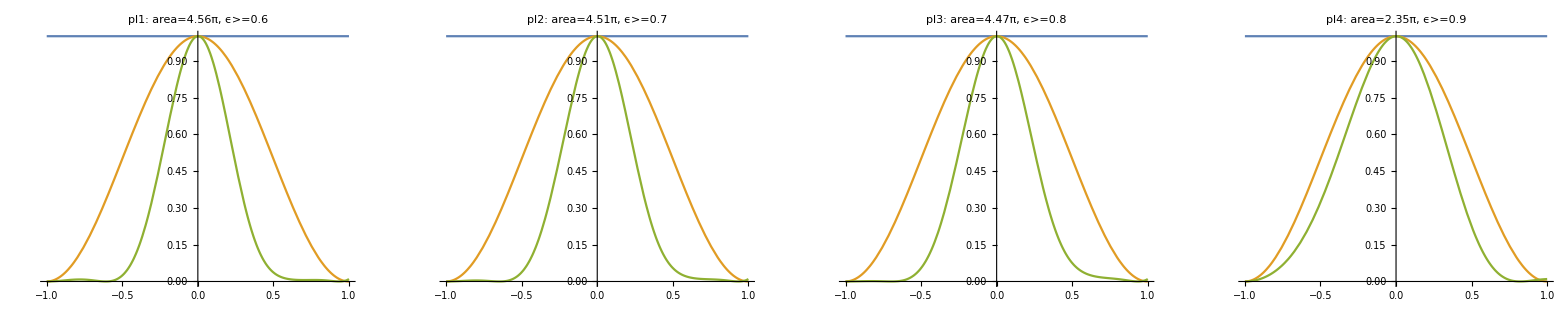

NB3; p=1/2, error=0.01

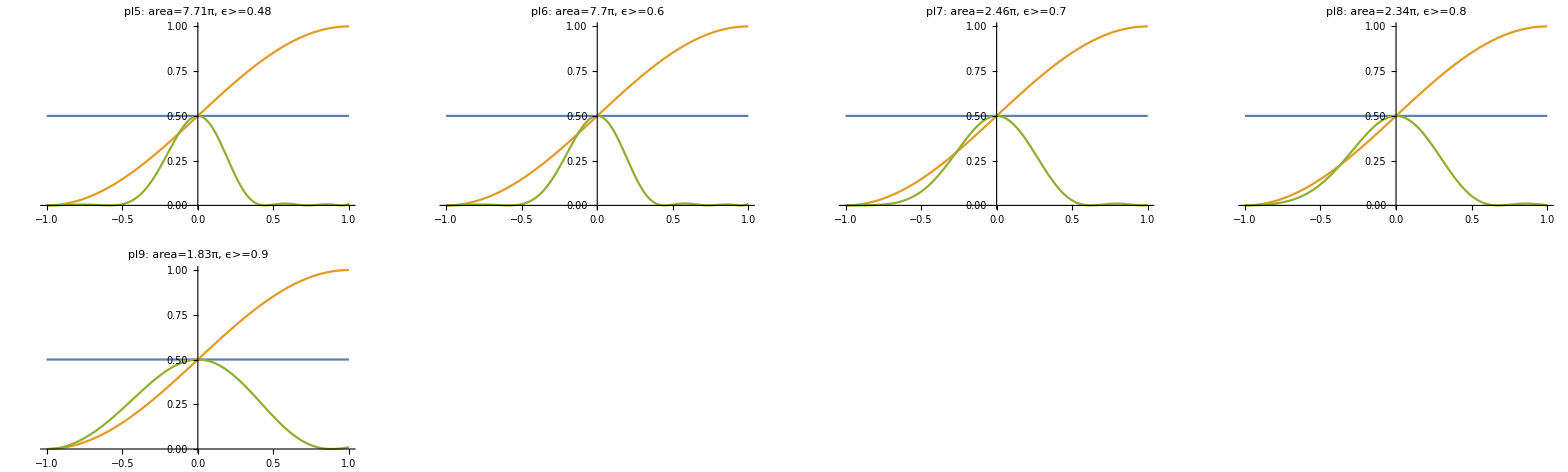

NB3; p=1/3, error=0.01

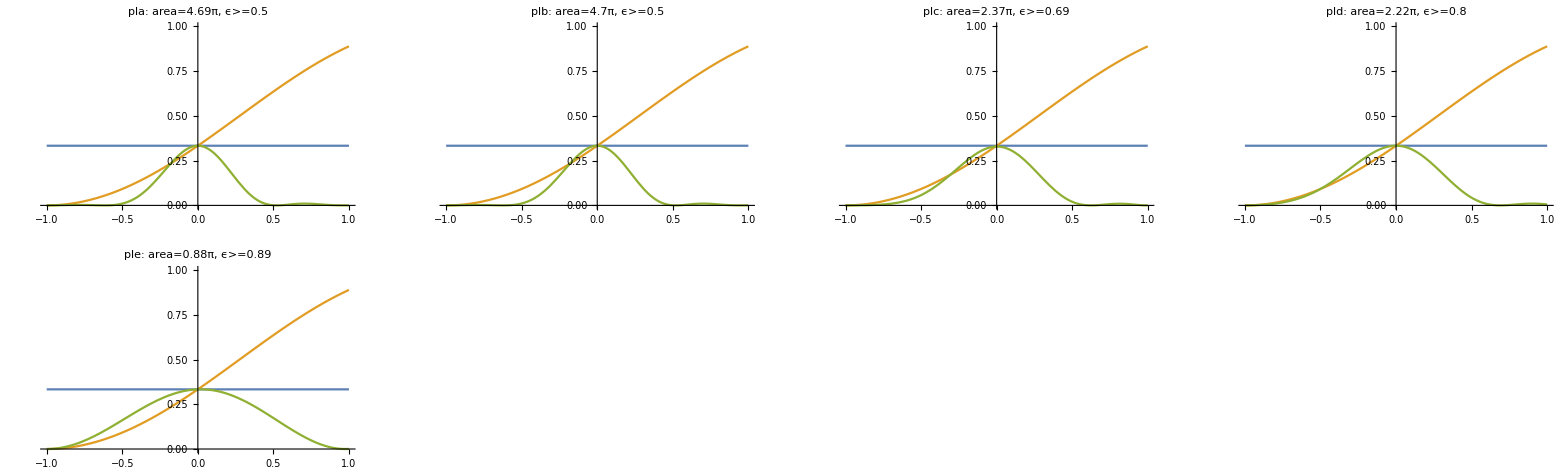

```mathematica
(*N=3*)
sequence=U[Δ1,Ω1].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,True]]

pl1=plt[1,{Δ1->-2.3076,Δ2->1.5884,Ω1->1.1822,Ω2->2.1955},"pl1"];
pl2=plt[1,{Δ1->2.3382,Δ2->-1.6353,Ω1->1.1684,Ω2->2.1747},"pl2"];
pl3=plt[1,{Δ1->-2.3665,Δ2->1.6859,Ω1->1.1584,Ω2->2.1546},"pl3"];
pl4=plt[1,{Δ1->-0.5520,Δ2->2.1401,Ω1->0.3756,Ω2->1.6016},"pl4"];

pl5=plt[1/2,{Δ1->9.9254,Δ2->1.7920,Ω1->2.7822,Ω2->2.1458},"pl5"];
pl6=plt[1/2,{Δ1->9.9279,Δ2->1.7927,Ω1->2.7743,Ω2->2.1466},"pl6"];
pl7=plt[1/2,{Δ1->-0.4675,Δ2->1.6841,Ω1->0.5642,Ω2->1.3326},"pl7"];
pl8=plt[1/2,{Δ1->-0.4713,Δ2->1.7606,Ω1->0.5603,Ω2->1.216},"pl8"];
pl9=plt[1/2,{Δ1->-0.5054,Δ2->1.9865,Ω1->0.5220,Ω2->0.7881},"pl9"];

pla=plt[1/3,{Δ1->4.3843,Δ2->1.6297,Ω1->1.2974,Ω2->2.0980},"pla"];
plb=plt[1/3,{Δ1->4.3715,Δ2->1.6407,Ω1->1.3082,Ω2->2.0826},"plb"];(*not a mistake*)
plc=plt[1/3,{Δ1->-0.5234,Δ2->1.721,Ω1->0.5850,Ω2->1.2008},"plc"];
pld=plt[1/3,{Δ1->-0.5365,Δ2->1.8048,Ω1->0.5721,Ω2->1.0775},"pld"];
ple=plt[1/3,{Δ1->1.272,Δ2->0.9935,Ω1->0.,Ω2->0.8793},"ple"];

GGrid[Text[Style["NB3; p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["NB3; p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8},{pl9}},ImageSize->Full]
GGrid[Text[Style["NB3; p=1/3"<> error,FontSize->20]],{{pla,plb,plc,pld},{ple}},ImageSize->Full]
```

NB4; p=1, error=0.01

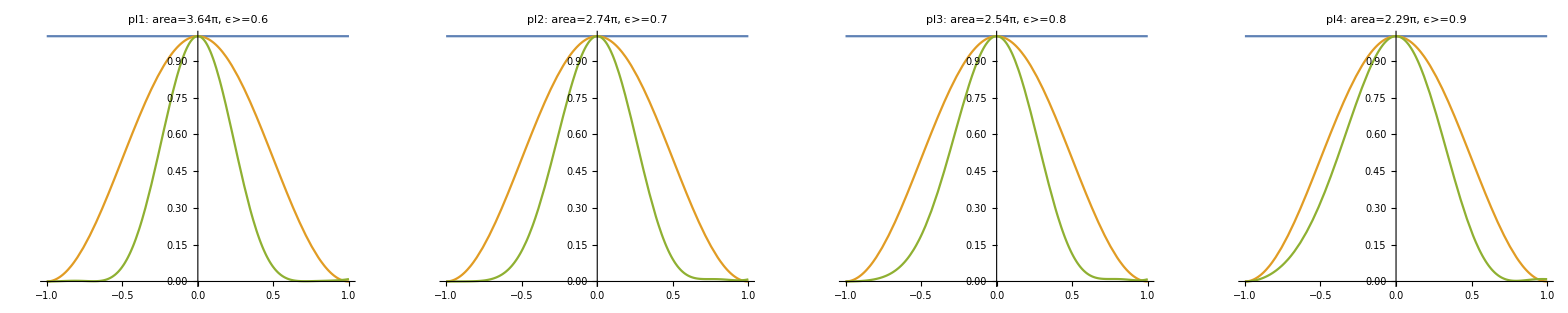

NB4; p=1/2, error=0.01

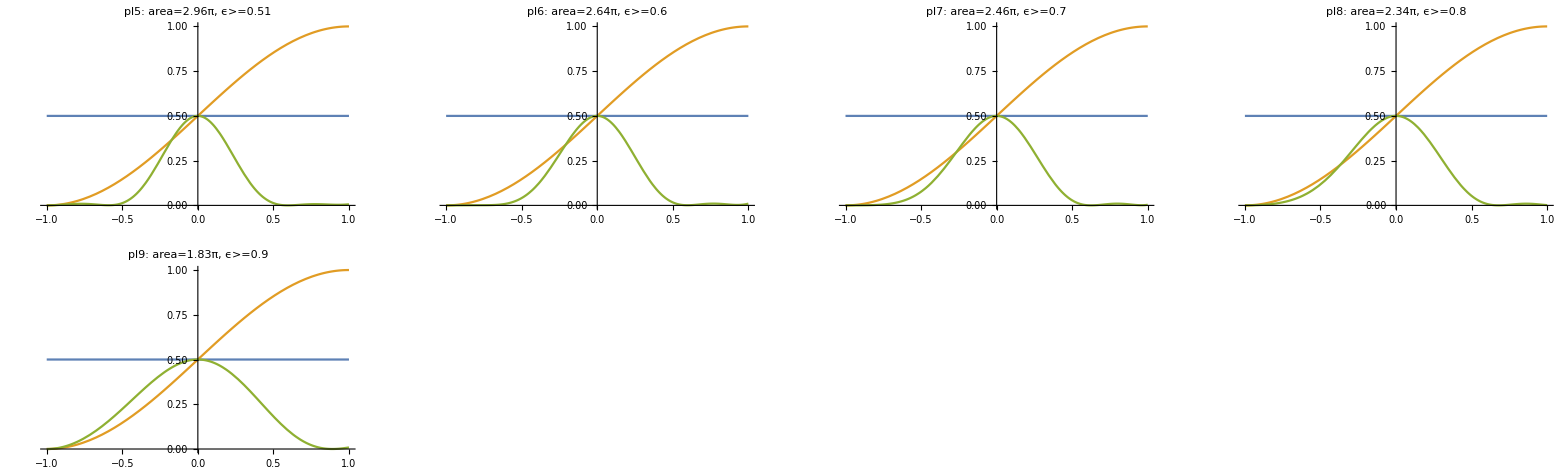

NB4; p=1/3, error=0.01

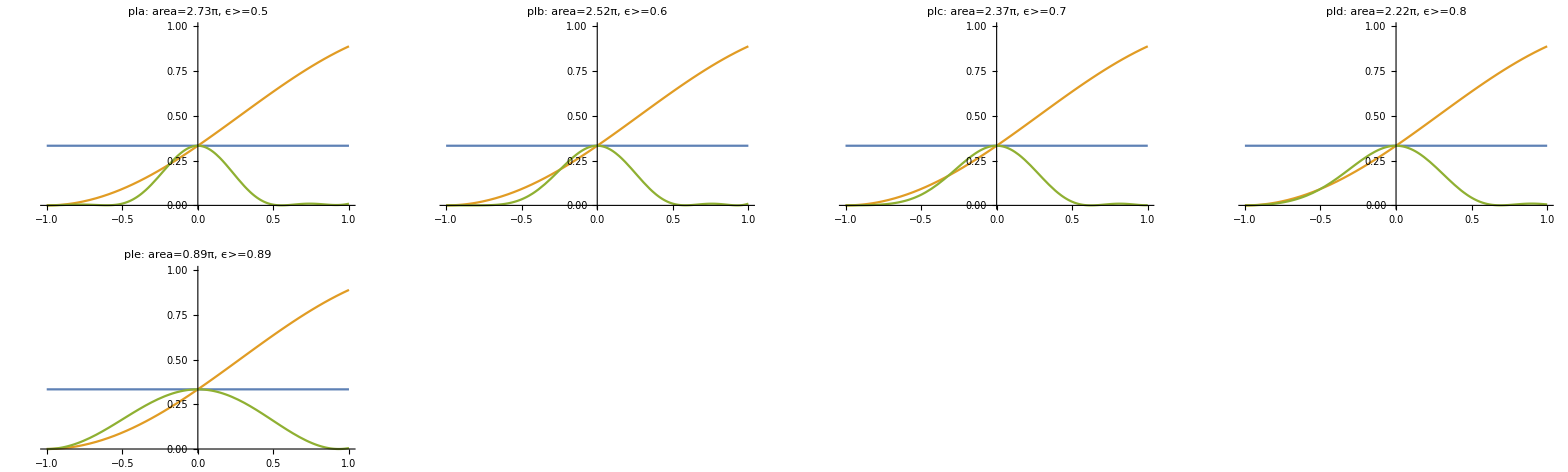

```mathematica
(*N=4*)
sequence=U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->2.3667,Δ2->-1.3045,Δ3->-0.4563,Δ4->0.6391,Ω1->1.0613,Ω2->1.7679,Ω3->0.2962,Ω4->0.5124},"pl1"];
pl2=plt[1,{Δ1->0.7595,Δ2->0.7483,Δ3->-0.3657,Δ4->0.6214,Ω1->1.3654,Ω2->0.1617,Ω3->0.4021,Ω4->0.8107},"pl2"];
pl3=plt[1,{Δ1->0.7377,Δ2->0.7216,Δ3->-0.1343,Δ4->0.5670,Ω1->1.1706,Ω2->0.2764,Ω3->0.4626,Ω4->0.6354},"pl3"];
pl4=plt[1,{Δ1->0.8300,Δ2->0.8223,Δ3->-0.0470,Δ4->0.5021,Ω1->0.9773,Ω2->0.3124,Ω3->0.4991,Ω4->0.4970},"pl4"];

pl5=plt[0.5,{Δ1->-0.2442,Δ2->0.2359,Δ3->-0.8526,Δ4->-0.3569,Ω1->0.8651,Ω2->0.5600,Ω3->0.0554,Ω4->1.4777},"pl5"];
pl6=plt[0.5,{Δ1->0.3492,Δ2->0.9230,Δ3->-0.2070,Δ4->0.2548,Ω1->1.2005,Ω2->0.2739,Ω3->0.4034,Ω4->0.7627},"pl6"];
pl7=plt[0.5,{Δ1->0.0945,Δ2->-0.4735,Δ3->1.6857,Δ4->-0.4591,Ω1->0.0099,Ω2->0.5466,Ω3->1.3346,Ω4->0.5710},"pl7"];
pl8=plt[0.5,{Δ1->-0.4440,Δ2->0.0838,Δ3->1.6292,Δ4->-0.4890,Ω1->0.4534,Ω2->0.2200,Ω3->1.1168,Ω4->0.5478},"pl8"];
pl9=plt[0.5,{Δ1->0.4643,Δ2->1.3090,Δ3->-0.3572,Δ4->0.2740,Ω1->0.6913,Ω2->0.3351,Ω3->0.3865,Ω4->0.4175},"pl9"];

pla=plt[1/3,{Δ1->0.2466,Δ2->0.9460,Δ3->-0.2090,Δ4->0.1938,Ω1->1.2709,Ω2->0.2242,Ω3->0.3775,Ω4->0.8550},"pla"];
plb=plt[1/3,{Δ1->-0.1573,Δ2->-0.4223,Δ3->1.7958,Δ4->-0.4995,Ω1->0.4352,Ω2->0.0544,Ω3->1.425,Ω4->0.6031},"plb"];
plc=plt[1/3,{Δ1->-0.5141,Δ2->1.6043,Δ3->0.1194,Δ4->-0.5309,Ω1->0.5925,Ω2->1.1200,Ω3->0.0806,Ω4->0.5799},"plc"];
pld=plt[1/3,{Δ1->-0.5517,Δ2->1.6848,Δ3->0.0263,Δ4->-0.4759,Ω1->0.5549,Ω2->0.9942,Ω3->0.2479,Ω4->0.4243},"pld"];
ple=plt[1/3,{Δ1->0.1278,Δ2->0.5376,Δ3->0.1003,Δ4->0.0453,Ω1->0.2381,Ω2->0.3875,Ω3->0.1132,Ω4->0.1494},"ple"];

GGrid[Text[Style["NB4; p=1"<>error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/2"<>error,FontSize->20]],{{pl5,pl6,pl7,pl8},{pl9}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/3"<>error,FontSize->20]],{{pla,plb,plc,pld},{ple}},ImageSize->Full]
```

NB5; p=1, error=0.01

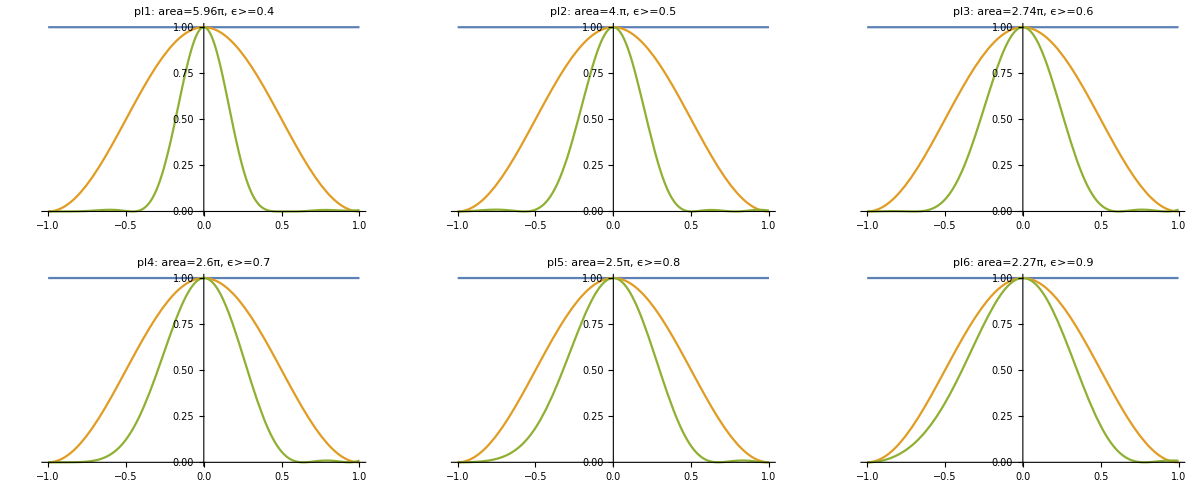

NB5; p=1/2, error=0.01

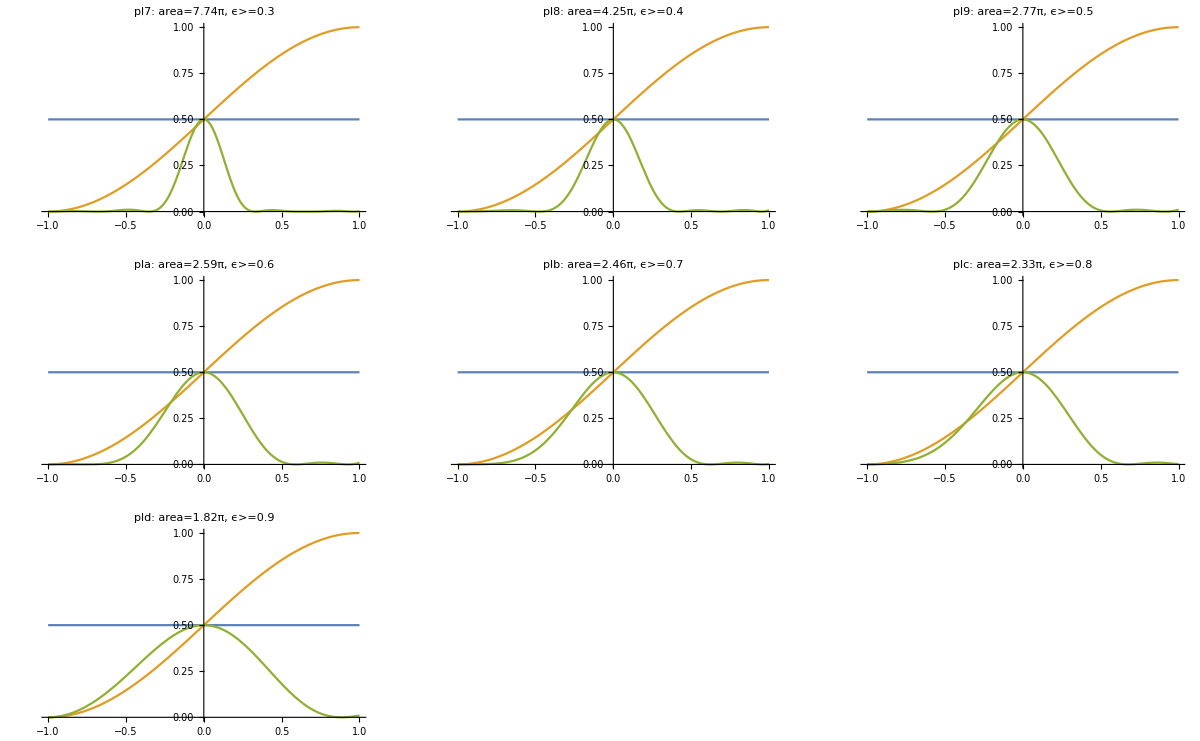

NB5; p=1/3, error=0.01

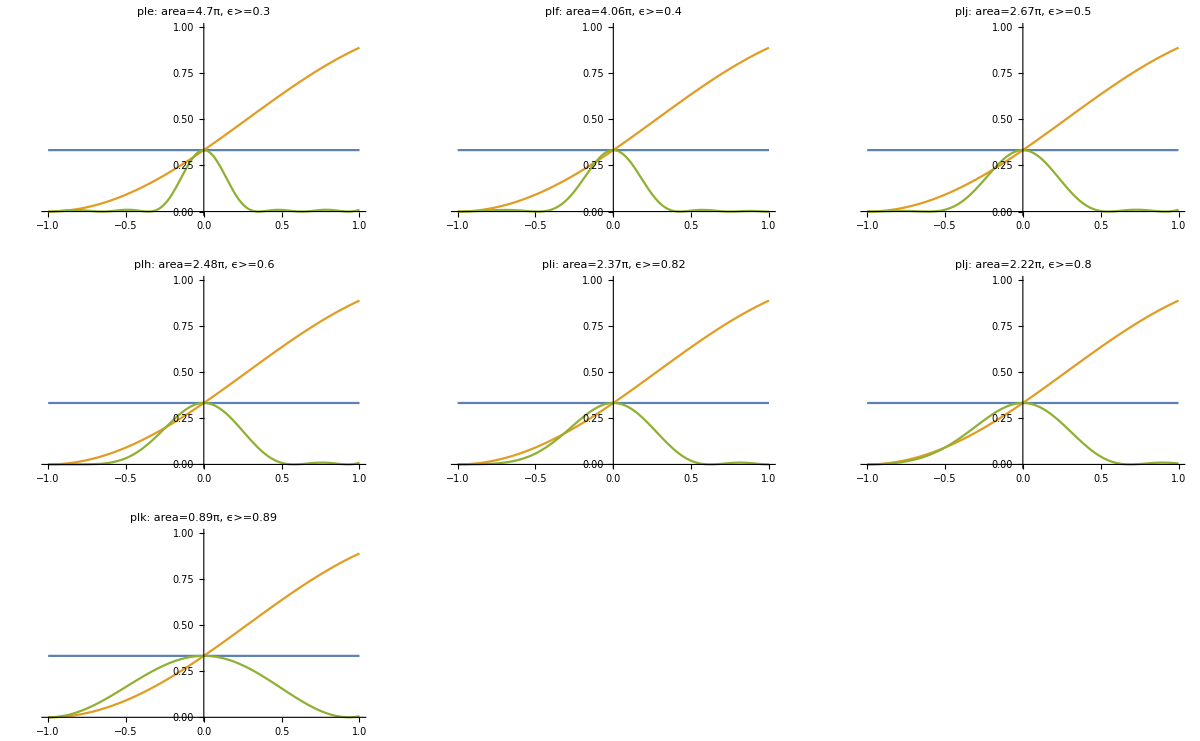

```mathematica
(*N=5*)
sequence=U[Δ1,Ω1].U[Δ2,Ω2].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,True]]

pl1=plt[1.0,{Δ1->1.3155,Δ2->2.2953,Δ3->-0.5687,Ω1->1.6971,Ω2->1.0058,Ω3->0.5506},"pl1"];
pl2=plt[1.0,{Δ1->-0.3562,Δ2->0.7541,Δ3->1.7141,Ω1->0.5252,Ω2->0.4416,Ω3->2.0703},"pl2"];
pl3=plt[1.0,{Δ1->0.5418,Δ2->-0.072,Δ3->0.9808,Ω1->0.4566,Ω2->0.4743,Ω3->0.8803},"pl3"];
pl4=plt[1.0,{Δ1->0.4071,Δ2->0.215,Δ3->0.7071,Ω1->0.3657,Ω2->0.7445,Ω3->0.3791},"pl4"];
pl5=plt[1.0,{Δ1->0.4652,Δ2->0.0588,Δ3->0.9063,Ω1->0.5258,Ω2->0.4636,Ω3->0.5168},"pl5"];
pl6=plt[1.0,{Δ1->0.4737,Δ2->0.095,Δ3->1.0052,Ω1->0.4924,Ω2->0.4208,Ω3->0.4392},"pl6"];

pl7=plt[0.5,{Δ1->2.6025,Δ2->1.5914,Δ3->2.7429,Ω1->0.8758,Ω2->2.1404,Ω3->1.7064},"pl7"];
pl8=plt[0.5,{Δ1->0.2135,Δ2->-0.5822,Δ3->1.894,Ω1->0.9401,Ω2->0.5006,Ω3->1.3732},"pl8"];
pl9=plt[0.5,{Δ1->0.7219,Δ2->0.0091,Δ3->0.8577,Ω1->0.4501,Ω2->0.348,Ω3->1.1725},"pl9"];
pla=plt[0.5,{Δ1->0.6843,Δ2->0.0988,Δ3->0.7988,Ω1->0.4684,Ω2->0.404,Ω3->0.8453},"pla"];
plb=plt[0.5,{Δ1->-0.0364,Δ2->0.8303,Δ3->0.0268,Ω1->0.4728,Ω2->0.4846,Ω3->0.5432},"plb"];
plc=plt[0.5,{Δ1->-0.0179,Δ2->0.8773,Δ3->0.0312,Ω1->0.4601,Ω2->0.4688,Ω3->0.4769},"plc"];
pld=plt[0.5,{Δ1->0.7518,Δ2->0.2132,Δ3->1.0185,Ω1->0.4532,Ω2->0.2738,Ω3->0.3679},"pld"];

ple=plt[1/3,{Δ1->0.7548,Δ2->0.8028,Δ3->0.2687,Ω1->0.3281,Ω2->1.4807,Ω3->1.0834},"ple"];
plf=plt[1/3,{Δ1->0.2993,Δ2->-0.6416,Δ3->1.9412,Ω1->0.8786,Ω2->0.559,Ω3->1.1886},"plf"];
plg=plt[1/3,{Δ1->0.7498,Δ2->0.0565,Δ3->0.8621,Ω1->0.4409,Ω2->0.326,Ω3->1.1406},"plj"];
plh=plt[1/3,{Δ1->-0.5023,Δ2->0.1094,Δ3->1.3533,Ω1->0.4989,Ω2->0.2198,Ω3->1.0441},"plh"];
pli=plt[1/3,{Δ1->-0.4369,Δ2->-0.0527,Δ3->1.6229,Ω1->0.4432,Ω2->0.1789,Ω3->1.1236},"pli"];
plj=plt[1/3,{Δ1->-0.5242,Δ2->0.1415,Δ3->1.44,Ω1->0.4848,Ω2->0.2039,Ω3->0.8385},"plj"];
plk=plt[1/3,{Δ1->0.0513,Δ2->0.1259,Δ3->0.453,Ω1->0.144,Ω2->0.1385,Ω3->0.3231},"plk"];

GGrid[Text[Style["NB5; p=1"<>error,FontSize->20]],{{pl1,pl2,pl3},{pl4,pl5,pl6}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/2"<>error,FontSize->20]],{{pl7,pl8,pl9},{pla,plb,plc},{pld}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/3"<>error,FontSize->20]],{{ple,plf,plg},{plh,pli,plj},{plk}},ImageSize->Full]
```